```mathematica
Quit[];
```

```mathematica
(*diseased state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*assume tau_s=tau_g*);
```

```mathematica
(* Rescaled System's coefficients and function definition *)
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_]:={
-u[[1]]+f1[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f2[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium point*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{20.4425,21.8366}

```mathematica
(*characteristic parameter values*)
alpha=ac*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-2.53928

11.2213

```mathematica
(*Strong Gamma kernel - Laplace transform and related functions defined in paper*)
H[z_]:=(2/(2+z))^2;
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2-w^2/2-(2 w^2)/t; (*given explicitely for ease of computation*)
be[t_,w_]:=1+w^2/2+w^2/t^2+w^4/16+w^4/(2 t^2)+w^6/(16 t^2); (*given explicitely for ease of computation*)
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=4/(4+w^2); (*given explicitely for ease of computation*)
theta[w_]:=2ArcTan[w/2]; (*given explicitely for ease of computation*)
w1[t_]:=2*Sqrt[1+t]; (*given explicitely for ease of computation*)
mu[w_]:=1/(rho[w]*Cos[theta[w]]);
```

```mathematica
(*No critical value of tau such that (alpha,beta) is exactly on the line (l_tau)*)
Solve[beta==-((tau+2)^2/tau)*(alpha+(tau+2)^2/tau),tau,Reals]
```

{}

```mathematica
(*only one critical value of tau where (alpha,beta) is on the curve (gamma_tau)*)
NSolve[{alpha==al[t,w],beta==be[t,w],t>0,w>0},{t,w}]
```

{{t→0.283222,w→0.774794}}

```mathematica
(*Use Theorem 2.8 to detect critical value of time delay and frequency - along the curve (gamma_tau)*)
{Tau,W}={t,w}/.NSolve[{alpha==al[t,w],beta==be[t,w],t>0,w>0},{t,w}][[1]]
```

{0.283222,0.774794}

```mathematica
(*predicted frequency of oscillations at Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=W/(Tau*2*Pi)
```

0.435391

```mathematica
(*frequency of oscillations at Hopf bifurcation - rescaled*)
freq/(tauS*10^(-3))
```

72.5652

```mathematica
(*stability region for Strong Gamma kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared - using inequalities in Example 2.2*)
ps[t_]:=
Show[RegionPlot[y>-(2+t)^2/t(x+(2+t)^2/t)&&y<((-8+(-4+x) t)^2 (-2 x+(2+t)^2))/(4 t (4+t)^3)&&y>x-1,{x,2*mu[w1[t]],2},{y,mu[w1[t]],0.96*mu[w1[t]]^2},PlotPoints->100],
Plot[x-1,{x,1+1/Co[t,w1[t]],2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"S. Gamma, τ=",t}],Bold,19],Background->LightYellow,RoundingRadius->4],{1+mu[w1[Tau]],0.85*mu[w1[Tau]]^2}],
PlotRange->{{2*mu[w1[Tau]],2},{mu[w1[Tau]],0.96*mu[w1[Tau]]^2}}]
```

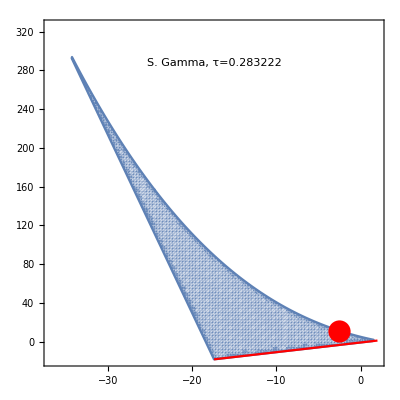

```mathematica
ps[Tau]
```

```mathematica
(*system with STRONG GAMMA kernel - using linear chain trick*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[2]],
ud1'[t]==2*(u[t]-ud1[t])/tau,
vd1'[t]==2*(v[t]-vd1[t])/tau,
ud2'[t]==2*(ud1[t]-ud2[t])/tau,
vd2'[t]==2*(vd1[t]-vd2[t])/tau,
u[0]==0,
v[0]==0,
ud1[0]==0,
vd1[0]==0,
ud2[0]==0,
vd2[0]==0};
```

```mathematica
(*numerical computation of frequency of oscillations*)
Tmax=2000;
pts[tau_]:=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[2]],
ud1'[t]==2*(u[t]-ud1[t])/tau,
vd1'[t]==2*(v[t]-vd1[t])/tau,
ud2'[t]==2*(ud1[t]-ud2[t])/tau,
vd2'[t]==2*(vd1[t]-vd2[t])/tau,
u[0]==eq[[1]]*RandomReal[{0.1,0.2}],
v[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud1[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd1[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud2[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd2[0]==eq[[2]]*RandomReal[{0.1,0.2}],
WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,0.8*Tmax,Tmax}]][[2,1]];
frequency[tau_]:=1/Mean[Differences[pts[tau],1,2]]
```

```mathematica
(*numerically computed frequency at Hopf bifurcation agrees with theoretically obtained value*)
frequency[Tau]/(tauS*10^(-3))
```

72.4853

```mathematica
pfreqStrong=Table[{del,frequency[del]/(tauS*10^(-3))},{del,Tau,4,0.05}];
```

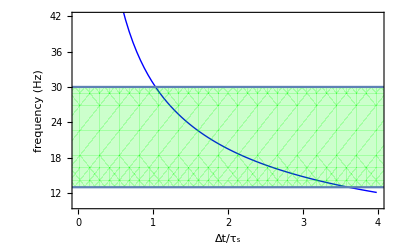

```mathematica
Show[ListPlot[pfreqStrong,Joined->True,PlotRange->All,PlotStyle->{Thick,Blue}],RegionPlot[13<y<30,{x,-0.5,4.5},{y,10,90},PlotStyle->{Green,Opacity[0.2]}],
FrameLabel->{"Δt/τ_s","frequency (Hz)"},Frame->True,Axes->False,PlotRange->{{0,4},{10,42}}]
```

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=100/1.2;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)/(tauS*10^(-3))],v[(t+trans)/(tauS*10^(-3))]} /. NDSolve[sys[tau],{u,v,ud1,vd1,ud2,vd2},{t,Tmax}]],{t,0,(Tmax-trans)*tauS*10^(-3)},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"STN, GP vs. time (s)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

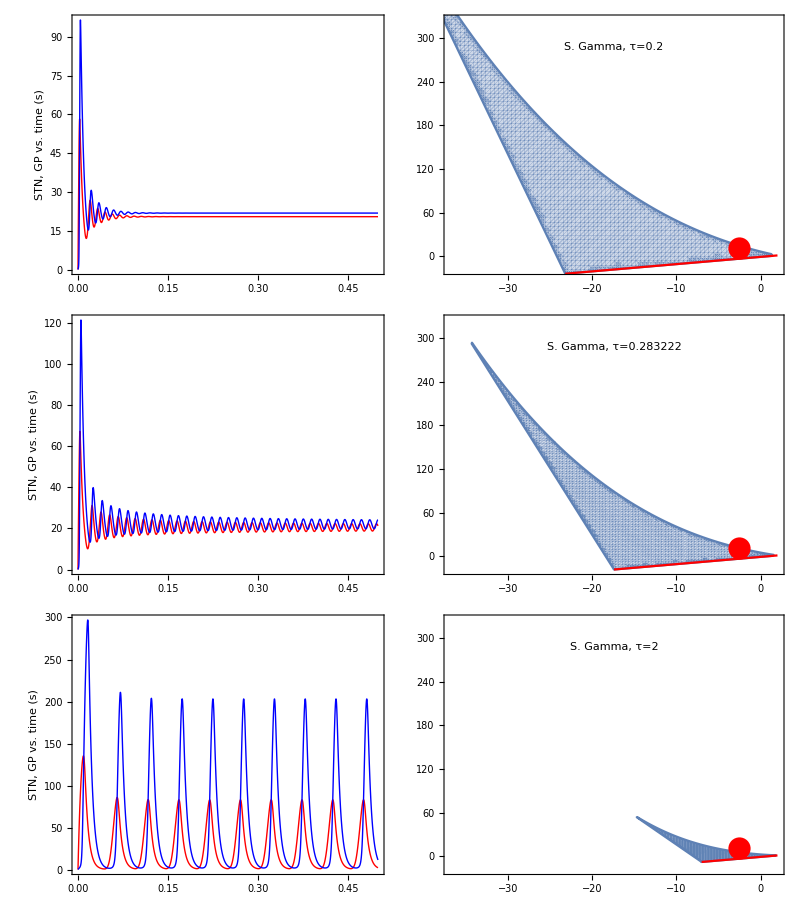

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[0.2],ps[0.2]},{p1[Tau],ps[Tau]},{p1[2],ps[2]}}]
```

```mathematica
Tmax = 100;
trans=0;
p2[tau_]:=ParametricPlot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v,ud1,vd1,ud2,vd2},{t,Tmax}]],{t,0,Tmax-trans},Axes->False,Frame->True,AspectRatio->1,PlotRange->All,PlotLabel->Row[Style[#,14] & /@{"τ=",tau}],LabelStyle->Directive[Bold,Black, Larger], (*ColorFunction->{Red, Blue}*) ColorFunction->(ColorData[{"LightTemperatureMap","Reversed"}][#3]&), ImageSize->{Automatic,300},FrameStyle->Directive[FontSize->14]]
```

```mathematica
Show[GraphicsGrid[{{p2[0.27],p2[Tau],p2[0.35]}}]]
```